# Esercizio b: sistema proprio LTI-TD

Immetto le matrici A, B, C

```mathematica
A={{-4/125, -204/125, 8/5}, {129/125, 329/125, -13/5}, {1, 2, -2}}
```

{{-4/125,-204/125,8/5},{129/125,329/125,-13/5},{1,2,-2}}

```mathematica
B={{1}, {-1}, {0}}
```

{{1},{-1},{0}}

```mathematica
Cc={{2, 2, -1}}
```

{{2,2,-1}}

## 1. Modi naturali del sistema

```mathematica
λ = Eigenvalues[A]
```

{2/5,2/5,-1/5}

La matrice presenta i seguenti autovalori:

con molteplicità algebrica pari a 2

con molteplicità algebrica pari a 1

Calcolo la molteplicità geometrica. Il calcolo viene eseguito per i soli autovalori con m.a. > 1:

```mathematica
NullSpace[A-(2/5)IdentityMatrix[3]]
```

{{14/15,11/15,1}}

Ottenendo che: 
                           m.a. (λ_1) = 2 ≠ m.g. (λ_1) = 1

Poichè molteplicità algebrica e geonetrica non coincidono, sono costretto ad utilizzare la forma canonica di Jordan. Utilizzando questa forma ottengo che la matrice A ∈ ℝ^(n×n) è simile, per tramite di una opportuna matrice T ∈ ℝ^(n×n) non singolare, ad una forma diagonale a blocchi:

A ∼^T  Λ_j

Calcolo il polinomio minimo per visualizzare il numero di modi:

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_]:=Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

```mathematica
Factor[MatrixMinimalPolynomial[A,x]]
```

1/125 (-2+5 x)^2 (1+5 x)

Avrò 3 modi naturali (grado del polinomio minimo)

Tramite questa funzione built-in di Mathematica riesco a ricavare la matrice di cambiamento di base (T) e la matrice di Jordan( Λ)

```mathematica
{T, Λ}=JordanDecomposition[A]
```

{{{-2/15,14/15,41/9},{29/30,11/15,-16/9},{1,1,0}},{{-1/5,0,0},{0,2/5,1},{0,0,2/5}}}

```mathematica
T//MatrixForm
```

(-2/15 | 14/15 | 41/9
29/30 | 11/15 | -16/9
1 | 1 | 0)

```mathematica
Λ
```

{{-1/5,0,0},{0,2/5,1},{0,0,2/5}}

Si identificano facilmente i blocchi di jordan sulla matrice: (-1/5 | 0 | 0
0 | 2/5 | 1
0 | 0 | 2/5)

I modi generati sono successioni polinomial-potenza e possono essere individuati sulla diagonale della matrice Λ̂:

```mathematica
Λ̂= MatrixPower[Λ,k]//MatrixForm
```

((-1/5)^k | 0 | 0
0 | (5/2)^-k | (5/2)^(1-k) k
0 | 0 | (5/2)^-k)

Modi: , ,

Li rappresneto graficamente:

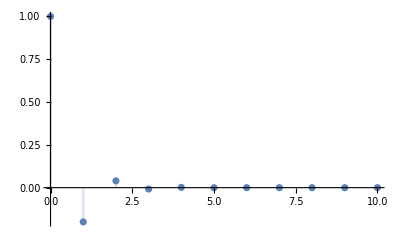

```mathematica
DiscretePlot[(-1/5)^k,{k,0,10},PlotRange->All]
```

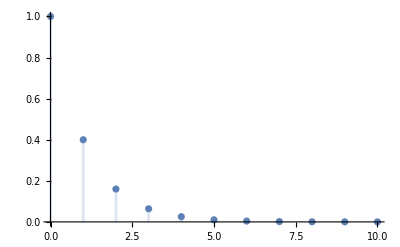

```mathematica
DiscretePlot[(2/5)^k,{k,0,10},PlotRange->All]
```

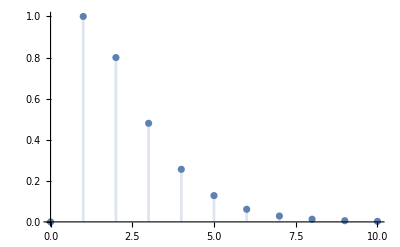

```mathematica
DiscretePlot[Binomial[k,1](2/5)^(k-1), {k,0,10},PlotRange->All]
```

```mathematica
T//MatrixForm
```

(-2/15 | 14/15 | 41/9
29/30 | 11/15 | -16/9
1 | 1 | 0)

```mathematica
Λ//MatrixForm
```

(-1/5 | 0 | 0
0 | 2/5 | 1
0 | 0 | 2/5)

Approfondimento: verifica che la prima e la seconda colonna di T siano autovettori standard della matrice A

Prima colonna, autovettore standard “agganciato” a (-1/5):

```mathematica
(A - (-1/5)IdentityMatrix[3]).T[[All,1]]
```

{0,0,0}

Seconda colonna, autovettore standard “agganciato” a (2/5):

```mathematica
(A - (2/5)IdentityMatrix[3]).T[[All,2]]
```

{0,0,0}

Catena sulla terza colonna:

```mathematica
T[[All,2]]
```

{14/15,11/15,1}

```mathematica
(A - (2/5)IdentityMatrix[3]).T[[All,3]]
```

{14/15,11/15,1}

Proprietà -> elevando al quadrato ottengo 0:

```mathematica
(A - (2/5)IdentityMatrix[3]).(A - (2/5)IdentityMatrix[3]).T[[All,3]]
```

{0,0,0}

## 2. Risposta libera

La risposta libera nello stato viene calcolata come: x_l(k)= T Λ^kz_0

```mathematica
x0 =({{3}, {-3}, {1}})
```

{{3},{-3},{1}}

```mathematica
z0 = Inverse[T].x0
```

{{16},{-15},{21/5}}

```mathematica
Subscript[x, l][t_]:=Simplify[T.MatrixPower[Λ,k].z0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(1/3 5^(-1-k) (-32 (-1)^k+77 2^k+147 2^k k)
1/6 5^(-1-k) (464 (-1)^k-277 2^(1+k)+231 2^k k)
1/2 5^-k (32 (-1)^k-15 2^(1+k)+21 2^k k))

Risposta libera nell’uscita

```mathematica
Subscript[y, l][t_]:= Simplify[Cc.Subscript[x, l][t]]
```

```mathematica
Subscript[y, l][t]//MatrixForm
```

(1/6 5^-k (64 (-1)^k-35 2^(1+k)+147 2^k k))

Modalità alternativa per calcolare la risposta libera nello stato: x_l(k)=  A^kx_0

```mathematica
Subscript[x, l][t_]:=Simplify[MatrixPower[A,k].x0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(1/3 5^(-1-k) (-32 (-1)^k+77 2^k+147 2^k k)
1/6 5^(-1-k) (464 (-1)^k-277 2^(1+k)+231 2^k k)
1/2 5^-k (32 (-1)^k-15 2^(1+k)+21 2^k k))

## 3. Configurazioni di stati iniziali che attivano sulla risp. libera alcuni modi naturali

```mathematica
T//MatrixForm
```

(-2/15 | 14/15 | 41/9
29/30 | 11/15 | -16/9
1 | 1 | 0)

```mathematica
Λ//MatrixForm
```

(-1/5 | 0 | 0
0 | 2/5 | 1
0 | 0 | 2/5)

```mathematica
x0 = 3({{-2/15}, {29/30}, {1}})
```

{{-2/5},{29/10},{3}}

```mathematica
z0 = Inverse[T].x0
```

{{3},{0},{0}}

```mathematica
Subscript[x, l][t_]:=Simplify[T.MatrixPower[Λ,k].z0]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-2 (-1)^k 5^(-1-k)
29/2 (-1)^k 5^(-1-k)
3 (-1/5)^k)

```mathematica
x0=4({{14/15}, {11/15}, {1}}) + 5({{41/9}, {-16/9}, {0}})
```

{{1193/45},{-268/45},{4}}

```mathematica
z0 = Inverse[T].x0
```

{{0},{4},{5}}

```mathematica
Subscript[x, l][t_]:=Simplify[Expand[T.MatrixPower[Λ,k].z0]]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(1/9 2^k 5^(-1-k) (1193+525 k)
1/9 2^(-1+k) 5^(-1-k) (-536+825 k)
2^(-1+k) 5^-k (8+25 k))

## 4. FdT, poli e zeri

A tempo discreto la risposta forzata è data da:

Dove  è la Funzione di Trasferimento G(z)

```mathematica
G[z_]:=Simplify[Cc.Inverse[z IdentityMatrix[3]-A].B]
```

```mathematica
G[z]
```

{{(125 (1+z))/((2-5 z)^2 (1+5 z))}}

E’ rispetta la condizione per cui il grado del numeratore è minore di quelo del denominatore (sempre verificata nei sistemi propri con D=0). Le radici del denominatore sono generalmente un sottoinsieme degli autovalori di A. In questo caso si nota che il denominatore è del tutto equivalente al polinomio caratteristico della matrice A e di conseguenza le radici del denominatore coincideranno con gli autovalori precedentemente trovati

```mathematica
CharacteristicPolynomial[A,z]
```

-4/125+(3 z^2)/5-z^3

Poli:

```mathematica
Solve[Denominator[G[z]]==0,z]
```

{{z→-1/5},{z→2/5},{z→2/5}}

Zeri :

```mathematica
Solve[Numerator[G[z]]==0,z]
```

{{z→-1}}

Verifico la validità dei risultati ottenuti provando a calcolare la FdT, i poli e gli zeri mediante un’apposita funzione built-in di mathematica:

```mathematica
Σ=StateSpaceModel[{A,B,Cc}]
```

-4/125-204/1258/51129/125329/125-13/5-112-2022-10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[Σ]
```

(-1-s)/(-4/125+(3 s^2)/5-s^3)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11-1-41FalseFalseFalseAutomaticNoneAutomatic

Così scritta si apprezza maggiormente al denominatore l’equivalenza con il polinomio caratteristico

```mathematica
TransferFunctionPoles[Σ]
```

{{{-1/5,2/5,2/5}}}

```mathematica
TransferFunctionZeros[Σ]
```

{{{-1}}}

## 5. Risposta al gradino

Il gradino unitario è quel segnale right sided definito come: 1(k) = Piecewise[{{1, k ≥0}, {0, k<0}}]

La Z-Trasformata del gradino unitario è z/(z-1) e posso anche verificarlo con Mathematica:

```mathematica
ZTransform[UnitStep[k],k,z]
```

z/(-1+z)

Sfruttando la relazione:  posso determinare la risposta forzata

```mathematica
Subscript[Y, f][z_]:=G[z](z/(z-1))
```

```mathematica
Subscript[Y, f][z]
```

{{(125 z (1+z))/((2-5 z)^2 (-1+z) (1+5 z))}}

Scritta così non può direttamente essere manipolata come la L-Trasformata scrivendo in fratti semplici. Per determinare l’antitrasformata Z devo effettuare un’altra operazione preliminare, che consiste nel dividere la risposta forzata così ottenuta per z:

```mathematica
(Subscript[Y, f][z])/z
```

{{(125 (1+z))/((2-5 z)^2 (-1+z) (1+5 z))}}

Otterrò dunque 4 fratti semplici (il grado del denominatore è 4):

```mathematica
Expand [Apart[(125 (1+z))/((2-5 z)^2 (-1+z) (1+5 z))]]
```

125/(27 (-1+z))-875/(9 (-2+5 z)^2)-125/(9 (-2+5 z))-250/(27 (1+5 z))

```mathematica
C1/(z-1)+C22/(z-2/5)^2+C21/(z-2/5)+C3/(z+1/5)
```

C1/(-1+z)+C22/(-2/5+z)^2+C21/(-2/5+z)+C3/(1/5+z)

Utilizzando la forma di Heaviside (non più semplificata) riesco a determinare i coefficienti incogniti:

C_ij= ,  dove v_i è la molteplicità algebrica e j è l’ordine

```mathematica
C1=lim_(z->1) (z-1) ((Subscript[Y, f][z])/z)[[1,1]]
```

125/27

Il termine C1 può anche essere calcolato sfruttando la relazione: C1 =

```mathematica
G[1]
```

{{125/27}}

```mathematica
C22=lim_(z->2/5) ((z-2/5)^2((Subscript[Y, f][z])/z))[[1,1]]
```

-35/9

```mathematica
C21=lim_(z->2/5) D[(z-2/5)^2((Subscript[Y, f][z])/z),z][[1,1]]
```

-25/9

```mathematica
C3 = lim_(z->-1/5) (z+1/5) ((Subscript[Y, f][z])/z)[[1,1]]
```

-50/27

```mathematica
C1/(z-1)+C22/(z-2/5)^2+C21/(z-2/5)+C3/(z+1/5)
```

125/(27 (-1+z))-35/(9 (-2/5+z)^2)-25/(9 (-2/5+z))-50/(27 (1/5+z))

```mathematica
C1(z/(z-1))+C22 z/(z-2/5)^2+C21 z/(z-2/5)+C3 z/(z+1/5)
```

(125 z)/(27 (-1+z))-(35 z)/(9 (-2/5+z)^2)-(25 z)/(9 (-2/5+z))-(50 z)/(27 (1/5+z))

Mi riconduco sempre alla forma:

```mathematica
YF[k_]:=C1 UnitStep[k]+C3 (-1/5)^k UnitStep[k]+  C21 (2/5)^k UnitStep[k]+ C22 k(2/5)^(k-1)UnitStep[k]
```

```mathematica
YF[k]
```

(125 UnitStep[k])/27-2/27 (-1)^k 5^(2-k) UnitStep[k]-1/9 2^k 5^(2-k) UnitStep[k]-7/9 2^(-1+k) 5^(2-k) k UnitStep[k]

Verifico la correttezza del risultato:

```mathematica
Expand[InverseZTransform[Subscript[Y, f][z],z,k]]
```

{{125/27-2/27 (-1)^k 5^(2-k)-1/9 2^k 5^(2-k)-7/9 2^(-1+k) 5^(2-k) k}}

La grafico:

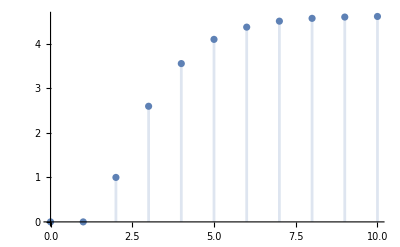

```mathematica
DiscretePlot[YF[k], {k,0,10}, PlotRange->All]
```

La risposta al gradino, scritta in maniera ornamentale, è dunque:

Nella risposta forzata possiamo evidenziare le due componenti che la caratterizzano:
- La risposta a regime, che è la componente legata all’ingresso: 125/271(k)

- La risposta transitoria, che è combinazione lineare di tutti i modi naturali ed à data dal secondo, terzo e quarto termine della risposta a gradino. La caratteristica di “transitorietà” è verificabile calcolando il limite per k tendente a infinito. Così facendo, poichè tutti i modi sono strettamente minori dell’unità, l’intera risposta transitoria tenderà a 0:

```mathematica
lim_(k->∞) (-50/27(-1/5)^k-25/9(2/5)^k-35/9 k(2/5)^(k-1))
```

0

Grafico assieme risposta a gradino e risposta a regime:

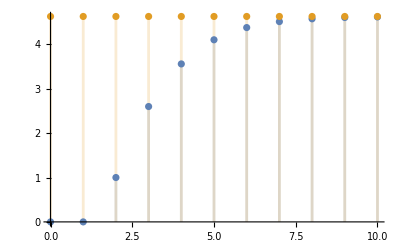

```mathematica
DiscretePlot[{YF[k],125/27 UnitStep[k]},{k,0,10}, PlotRange->All]
```

La risposta forzata si assesta sulla componente di regime

## 6.1 Modello ARMA

Partendo dal sistema SISO LTI-TD scritto in forma I/S/U come:

Piecewise[{{x (k+1), = A x(k) + B u(k)}, {y (k), = C x(k) + D u(k)}}]

Voglio determinare il suo modello ARMA equivalente. Per farlo sfrutto la seguente identità:

```mathematica
G[z][[1,1]]
```

(125 (1+z))/((2-5 z)^2 (1+5 z))

Valutandola come identità algebrica nel dominio della variabile complessa z ho che:

Che effettuando le opportune semplificazioni viene scritta come:

Sfrutto il teorema dell’anticipo di ordine n sulla Z-Trasformata (teorema dello shifting sinistro) per portare l’identità dal dominio della variabile complessa z al dominio di k
Conoscendo che, per il teorema dell’anticipo elementare ho:

Estendendolo ad n, posso scrivere che:

Nel caso considerato ottengo la seguente rappresentazione I/U del sistema, cioè il modello ARMA equivalente:

Incapsulo l’equazione differenziale appena trovata in Mathematica:

```mathematica
EquiDiff= 4y[k]-75y[k+2]+125y[k+3]==125u[k]+125u[k+1]
```

4 y[k]-75 y[2+k]+125 y[3+k]==125 u[k]+125 u[1+k]

```mathematica
Zt = ZTransform[EquiDiff,k,z]
```

4 ZTransform[y[k],k,z]-75 (-z^2 y[0]-z y[1]+z^2 ZTransform[y[k],k,z])+125 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 ZTransform[y[k],k,z])==125 ZTransform[u[k],k,z]+125 (-z u[0]+z ZTransform[u[k],k,z])

```mathematica
Zt/.{ZTransform[y[k],k,z]->Y[z], ZTransform[u[k],k,z]->U[z], u[0]->0}
```

4 Y[z]-75 (-z^2 y[0]-z y[1]+z^2 Y[z])+125 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y[z])==125 U[z]+125 z U[z]

Per risolvere l’equazione differenziale devo imporre le condizioni iniziali

```mathematica
x0=({{2}, {-1}, {2}})
```

{{2},{-1},{2}}

```mathematica
Cc
```

{{2,2,-1}}

```mathematica
y[0]=(Cc.x0)[[1,1]]
```

0

```mathematica
y[1]=(Cc.A.x0)[[1,1]]
```

2

```mathematica
y[2]=(Cc.A.A.x0)[[1,1]]
```

596/125

Ricalcolo Zt sostituendo i termini appena trovati:

```mathematica
nuova = 4 Y[z]-75 (-z^2 y[0]-z y[1]+z^2 Y[z])+125 (-z^3 y[0]-z^2 y[1]-z y[2]+z^3 Y[z])==125 U[z]+125 z U[z]
```

4 Y[z]-75 (-2 z+z^2 Y[z])+125 (-(596 z)/125-2 z^2+z^3 Y[z])==125 U[z]+125 z U[z]

```mathematica
Solve[nuova,Y[z]][[1,1]]
```

Y[z]→(446 z+250 z^2+125 U[z]+125 z U[z])/((-2+5 z)^2 (1+5 z))

Pongo U[z] = 1 ottendo

Calcolo ora l’antitrasformata Z della funzione di trasferimento precedentemente calcolata. Come concluso dai risultati ottenuti durante il corso infatti, la risposta all’impulso non è altro che l’antitrasformata Z della FdT (o a TC l’antitrasformata di Laplace).

```mathematica
g[k_]:=InverseZTransform[(446 z+250 z^2+125 +125 z)/((-2+5 z)^2 (1+5 z)),z,k]
```

```mathematica
g[k]
```

-1/36 5^(-1-k) (416 (-1)^k+5209 2^k-5901 2^k k) (1-UnitStep[-k])

La plotto

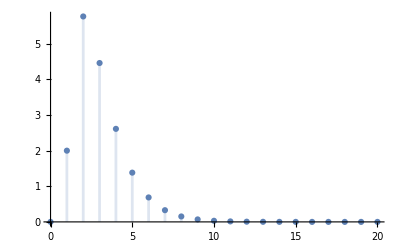

```mathematica
DiscretePlot[g[k],{k,0,20},PlotRange->All]
```

## 6.2 Risposta all’ingresso u(k)

```mathematica
u[k_]:=Piecewise[{{1,0<=k<=10}},0]
```

```mathematica
u[k]
```

Piecewise[{{1, 0≤k≤10}, {0, True}}]

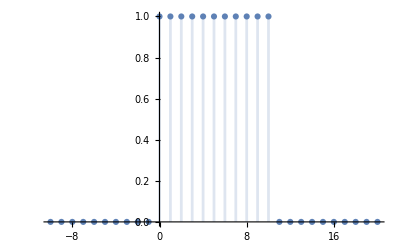

```mathematica
DiscretePlot[u[k],{k,-10,20},PlotRange->All]
```

```mathematica
yf[k_]:=∑_(n=0)^k g[k]×u[k-n]
```

```mathematica
yf[k]
```

Piecewise[{{-11/36 5^(-1-k) (416 (-1)^k+5209 2^k-5901 2^k k), k>10}, {1/36 5^(-1-k) (1+k) (-416 (-1)^k-5209 2^k+5901 2^k k), 0<k≤10}, {0, True}}]

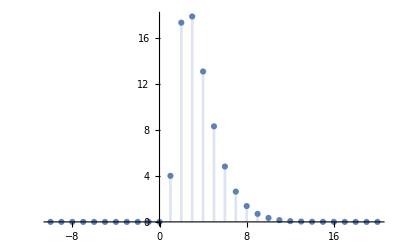

```mathematica
DiscretePlot[yf[k],{k,-10,20},PlotRange->All]
```

## 7. Stato iniziale che fa coincidere la risposta a gradino con quella a regime

```mathematica
x0={{x1},{x2},{x3}}
```

{{x1},{x2},{x3}}

```mathematica
Y[z]=(446z+250 z^2+125U[z]+125z U[z])/((-2+5z)^2(1+5z))
```

(446 z+250 z^2+125 U[z]+125 z U[z])/((-2+5 z)^2 (1+5 z))

```mathematica
U[z]=z/(z-1)
```

z/(-1+z)

```mathematica
Y[z]
```

(446 z+(125 z)/(-1+z)+250 z^2+(125 z^2)/(-1+z))/((-2+5 z)^2 (1+5 z))

```mathematica
G[z]
```

{{(125 (1+z))/((2-5 z)^2 (1+5 z))}}

```mathematica
regime = G[1]U[z]
```

{{(125 z)/(27 (-1+z))}}

```mathematica
transitoria=Factor[Y[z]-regime][[1]][[1]]
```

-(z (-9167-500 z+15625 z^2))/(27 (-2+5 z)^2 (1+5 z))

```mathematica
libera=Simplify[z Cc.Inverse[z IdentityMatrix[3]-A].x0][[1]][[1]]
```

(z (25 x3 (8+3 z-5 z^2)+2 x2 (-102-75 z+125 z^2)+x1 (-79-25 z+250 z^2)))/((2-5 z)^2 (1+5 z))

```mathematica
numeratore = Numerator[Simplify[Expand[libera+transitoria]]]
```

z (9167+5400 x3+500 z+2025 x3 z-15625 z^2-3375 x3 z^2+54 x2 (-102-75 z+125 z^2)+27 x1 (-79-25 z+250 z^2))

```mathematica
CF= CoefficientList[numeratore,z]
```

{0,9167-2133 x1-5508 x2+5400 x3,500-675 x1-4050 x2+2025 x3,-15625+6750 x1+6750 x2-3375 x3}

```mathematica
Solve[CF=={0,0,0,0}, {x1,x2,x3}]
```

{{x1→71/27,x2→-71/54,x3→-2}}

Stato così trovato:

```mathematica
x0={{71/27},{-71/54},{-2}}//MatrixForm
```

(71/27
-71/54
-2)

```mathematica
prova=StateSpaceModel[{A,B,Cc},SamplingPeriod->1]
```

-4/125-204/1258/51129/125329/125-13/5-112-2022-101StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
FullSimplify[OutputResponse[{prova,{71/27,-71/54,-2}},1,k],k∈Integers][[1,1]]
```

125/27

```mathematica
regimeInK=Expand[InverseZTransform[regime,z,k]][[1,1]]
```

125/27